# Nakagami channel data fitting

This notebook performs data fitting for the Nakagami channel model.

### Copyright notice

Copyright (C) 2012 Donagh Horgan.
Email: donaghh@rennes.ucc.ie.

This program is free software : you can redistribute it and/or modify
it under the terms of the GNU General Public License as published by
the Free Software Foundation, either version 3 of the License, or
(at your option) any later version.

This program is distributed in the hope that it will be useful,
but WITHOUT ANY WARRANTY; without even the implied warranty of
MERCHANTABILITY or FITNESS FOR A PARTICULAR PURPOSE. See 
COPYING for more details.

You should have received a copy of the GNU General Public License
along with this program. If not, see http://www.gnu.org/licenses.

### Version information

02/08/2012
1.0

### Changelog

Version 1.0: This version was used in the submitted version of the paper.

## Set up

Clear all symbol values and load function definitions:

```mathematica
ClearAll["Global`*"];
```

```mathematica
SetDirectory[NotebookDirectory[]];
<<definitions.m
<<plots.m
```

## Variables

Here, we define the ranges of values to be used for each parameter.

```mathematica
channelType="Nakagami";
mRange=Range[0.5,2,0.25];
precision=∞;
nRange={1,2,3,4,5,10,20,50};
snrdbRange=Range[0,-21,-1];
snrRange=10^(snrdbRange/10);
pf=0.1;
pd=0.9;
```

## Data fitting

Generate data and fit it to the model:

```mathematica
data=Flatten[Table[{m,n,γ,SampleComplexity[γ,pf,pd,n,ChannelType->{channelType,m},DatabaseLookup->True]},{m,mRange},{n,nRange},{γ,snrRange}],2];
```

```mathematica
model=(a ⅇ^(b/(m n))+(c+(d/(m n)^e))γ+f+(g/(m n)^h))SampleComplexity[γ,pf,pd,n,ChannelType->"AWGN"];
```

```mathematica
fit=FindFit[data,model,{{a,1},{b,Pi},c,d,{e,9},f,g,{h,9}},{m,n,γ},MaxIterations->10000]
```

FindFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

{a→0.953638,b→3.16447,c→1.39815,d→0.679112,e→3.59613,f→0.0973942,g→0.322522,h→9.07618}

```mathematica
modelf=Function[{m,n,γ},Evaluate[model/.fit]];
```

Calculate various error metrics:

```mathematica
{w,x,y,z}=Transpose[data];
```

```mathematica
exact=z;
approx=Apply[modelf,{w,x,y}];
```

```mathematica
error=exact-approx;
absError=Abs[error];
relError=error/exact;
absRelError=Abs[relError];
```

## Results

### Error statistics

#### Error and absolute error

Probability density function of the approximation error:

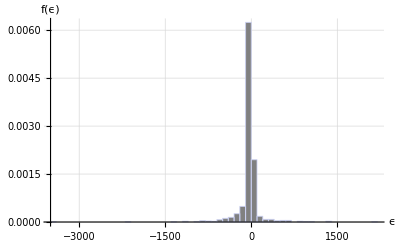

```mathematica
CustomHistogram[error,{"ϵ","f(ϵ)"}]
```

Histogram statistics:

```mathematica
StatsTable[error]
```

| μ | σ
 | -25.7592 | 231.415

```mathematica
StatsTable[absError]
```

| μ | σ
 | 82.3692 | 217.777

Largest errors:

```mathematica
MaxErrorsTable[absError,10]
```

γ (dB) | n | m | ϵ | ϵ_r
-21. | 1. | 1.25 | -3452.3 | -0.00136704
-21. | 1. | 2. | 2162.29 | 0.00218138
-20. | 1. | 1.25 | -2138.19 | -0.00134148
-21. | 1. | 1. | 1353.32 | 0.000282296
-20. | 1. | 2. | 1339.53 | 0.00214049
-21. | 2. | 1.25 | 1334.39 | 0.00365847
-19. | 1. | 1.25 | -1317.02 | -0.00130906
-21. | 1. | 1.5 | -1198.06 | -0.000721402
-21. | 5. | 2. | -1140.97 | -0.0197129
-21. | 4. | 2. | -1118.18 | -0.014287

#### Relative error and absolute relative error

Probability density function of the relative approximation error:

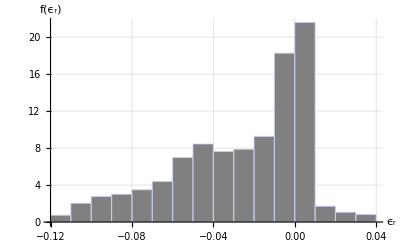

```mathematica
CustomHistogram[relError,{"ϵ_r","f(ϵ_r)"}]
```

Histogram statistics:

```mathematica
StatsTable[relError]
```

| μ | σ
 | -0.0266708 | 0.0318303

```mathematica
StatsTable[absRelError]
```

| μ | σ
 | 0.0291138 | 0.0296104

Largest relative errors:

```mathematica
MaxErrorsTable[absRelError,10]
```

γ (dB) | n | m | ϵ | ϵ_r
-3. | 50. | 2. | -0.190679 | -0.113906
-3. | 50. | 1.75 | -0.189858 | -0.113045
-4. | 50. | 2. | -0.273776 | -0.112085
-3. | 50. | 1.5 | -0.188766 | -0.111905
-4. | 50. | 1.75 | -0.272647 | -0.111234
-2. | 50. | 2. | -0.129532 | -0.111018
-3. | 50. | 1.25 | -0.187238 | -0.110323
-2. | 50. | 1.75 | -0.128922 | -0.110159
-4. | 50. | 1.5 | -0.271145 | -0.110109
-2. | 50. | 1.5 | -0.128109 | -0.109022